# MatchQ on Alternatives

```mathematica
s=FO["foo","bar1"|"bar2",Opt["baz"]];
```

```mathematica
s//FullForm
```

FO["foo",Alternatives["bar1","bar2"],Opt["baz"]]

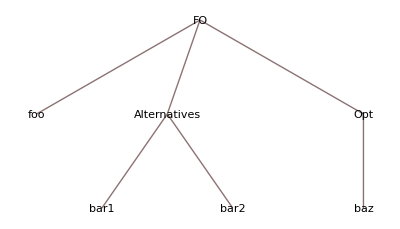

```mathematica
s//TreeForm
```

```mathematica
?MatchQ
```

MatchQ[expr,form] returns True if the pattern form matches expr, and returns False otherwise.

```mathematica
MatchQ[123,{_,_}]
MatchQ[{123,456},{_,_}]
MatchQ[{_,_},{_,_}]
```

False

True

True

```mathematica
MatchQ[s,s]
```

False

```mathematica
MatchQ[s,FO["foo",_,_]]
```

True

```mathematica
s2=head["y"|"x"];
```

```mathematica
FullForm[s2]
```

head[Alternatives["y","x"]]

```mathematica
MatchQ[s2,_[Verbatim[Alternatives][_String,"x"]]]
```

True

```mathematica
MatchQ[s2,_[_String|"x"]]
```

False

```mathematica
MatchQ[s2,_[a_]/;Head[a]==Alternatives]
```

True

```mathematica
MatchQ[s2,_[a_]/;(Head[a]==Alternatives&&MatchQ[a,_[_String,"x"]])]
```

True